```mathematica
(* Stability of MMI1 Model by the Routh-Hurwitz Criterion *)
(* //////// *)

(* Defining ODE, computing the Jacobian matrix and the characteristic polynomial *)
xvec = {R, r,C1, C1ʹ};
(* Using notations kon, kon2, koff, koff2 for now *) 
RHS = {σ - kon*R*r - kon2*R*r+koff*C1+koff2*C1ʹ-R+β1*γ*C1+β1ʹ*γʹ*C1ʹ, 
1-kon*R*r-kon2*R*r+koff*C1+koff2*C1ʹ-γ*r+α1*C1+α1ʹ*C1ʹ, 
kon*R*r-koff*C1-α1*C1-β1*γ*C1, 
kon2*R*r-koff2*C1ʹ-α1ʹ*C1ʹ-β1ʹ*γʹ*C1ʹ
};
RHS = RHS /. kon -> Superscript[κ, on] /. koff -> Superscript[κ, off] /. kon2 -> Superscript[κ, onʹ] /. koff2 -> Superscript[κ, offʹ] ; 
Jac =Grad[RHS, xvec];
charpol = Collect[CharacteristicPolynomial[Jac,λ],λ]; 

StringForm["Jacobian Matrix for C2KO model is ``.", MatrixForm[Jac]]
StringForm["Characteristic polynomial det(Jac-λ) = ``", charpol]

(* Extracting symbolic coefficients of the characteristic polynomial 
p(λ) = = a4*λ^4 + a3*λ^3 + a2*λ^2 + a1*λ + a0 *) 
a0 = Expand[Assuming[λ==0, Simplify[charpol]]];  
a1 = Expand[Assuming[λ==0, Simplify[(charpol-a0)/λ]]]; 
a2 = Expand[Assuming[λ==0, Simplify[(charpol-a0-a1*λ)/λ^2]]]; 
a3 = Assuming[λ==0, Simplify[(charpol-a0-a1*λ-a2*λ^2)/λ^3]]; 
a4 = Assuming[λ==0, Simplify[(charpol-a0-a1*λ-a2*λ^2-a3*λ^3)/λ^4]];
```

Jacobian Matrix for C2KO model is (-1-r κ-r κ | -R κ-R κ | β1 γ+κ | β1ʹ γʹ+κ
-r κ-r κ | -γ-R κ-R κ | α1+κ | α1ʹ+κ
r κ | R κ | -α1-β1 γ-κ | 0
r κ | R κ | 0 | -α1ʹ-β1ʹ γʹ-κ).

Characteristic polynomial det(Jac-λ) = …

```mathematica
(* Routh-Hurwitz Stability Criterion for deg 4 polynomial: First check that a4 > 0. Then stable if and only if a3 > 0, a0 > 0, u = a2*a3-a4*a1 > 0 and v = u*a1 - a3^2*a0 > 0 *) 

If[a4 < 0, 
a0 = -a0; 
a1 = -a1;
a2 = -a2;
a3 = -a3;
a4 = -a4; 
Print["Initially a4 < 0, so flip signs of all coefficients. Now a4 > 0. Continuing to check inequalities."]
]
Print["Successfully checked that a4 > 0. Continuing to check inequalities."]

StringForm["Checking that a3 > 0:
a3 = ``", a3]
```

Successfully checked that a4 > 0. Continuing to check inequalities.

Checking that a3 > 0:
a3 = 1+α1+α1ʹ+γ+β1 γ+β1ʹ γʹ+κ+κ+r κ+R κ+r κ+R κ

Checking that a0 > 0:

α1 α1ʹ γ+α1ʹ β1 γ^2+α1 β1ʹ γ γʹ+β1 β1ʹ γ^2 γʹ+α1ʹ γ κ^off+β1ʹ γ γʹ κ^off+α1 γ κ^offʹ+β1 γ^2 κ^offʹ+γ κ^off κ^offʹ+(r α1 α1ʹ γ+R α1ʹ β1 γ+r α1 β1ʹ γ γʹ+R β1 β1ʹ γ γʹ+r α1 γ κ^offʹ+R β1 γ κ^offʹ) κ^on+r α1 α1ʹ γ κ^onʹ+r α1ʹ β1 γ^2 κ^onʹ+R α1 β1ʹ γʹ κ^onʹ+R β1 β1ʹ γ γʹ κ^onʹ+r α1ʹ γ κ^off κ^onʹ+R β1ʹ γʹ κ^off κ^onʹ

The constant term is 0.

For deg 1 terms, the min coefficient is 0, min-nonzero is ∞, and max is 0.

For deg 2 terms, the min coefficient is 0, min-nonzero is ∞, and max is 0.

For deg 3 terms, the min coefficient is 0, min-nonzero is 1, and max is 1.

For deg 4 terms, the min coefficient is 0, min-nonzero is 1, and max is 1.

For deg 5 terms, the min coefficient is 0, min-nonzero is 1, and max is 1.

For deg 6 terms, the min coefficient is 0, min-nonzero is 1, and max is 1.

Listing all coefficients:

The constant term is 0

The non-zero coefficients of deg 1 terms are:

{_}→0

The non-zero coefficients of deg 2 terms are:

{_,_}→0

The non-zero coefficients of deg 3 terms are:

{1,3,8}→1
{1,2,3}→1
{2,3,7}→1
{3,7,8}→1
{_,_,_}→0

The non-zero coefficients of deg 4 terms are:

{1,3,5,6}→1
{2,3,3,4}→1
{3,3,4,8}→1
{3,5,6,7}→1
{_,_,_,_}→0

The non-zero coefficients of deg 5 terms are:

{1,5,6,11,12}→1
{1,3,8,9,10}→1
{1,2,3,9,10}→1
{1,2,3,9,12}→1
{2,3,7,9,12}→1
{2,3,4,10,11}→1
{3,3,4,5,6}→1
{3,4,8,10,11}→1
{5,6,7,11,12}→1
{_,_,_,_,_}→0

The non-zero coefficients of deg 6 terms are:

{1,3,5,6,9,10}→1
{2,3,3,4,9,12}→1
{3,4,5,6,10,11}→1
{3,4,5,6,11,12}→1
{_,_,_,_,_,_}→0

Empty histogram not generated for deg 0.

Empty histogram not generated for deg 1.

Empty histogram not generated for deg 2.

Generating all histograms:

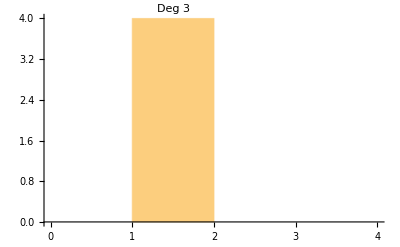
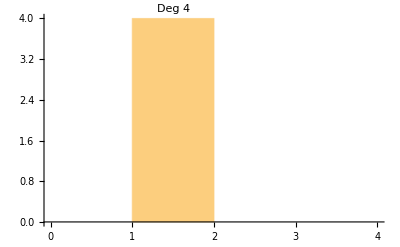
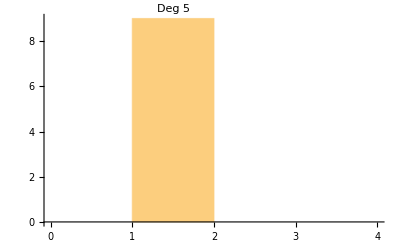
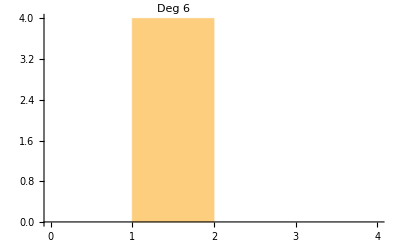

The number of non-zero coeff totals 21.

```mathematica
(* a0 > 0 *) 
Print[" 
Checking that a0 > 0: "]
Print[Collect[a0,Superscript[κ, on] ]]; 
coeff = CoefficientArrays[a0, Variables[a0]]; 


For[i=1, i <= Length[coeff], i++, (*Printing min/max coefficients*)
If[i==1,
Print[StringForm["The constant term is ``.", coeff[[1]]]];
];
If[i>1,
Print[StringForm["For deg `` terms, the min coefficient is ``, min-nonzero is ``, and max is ``.", i-1,  Min[coeff[[i]]],  Min[coeff[[i]]["NonzeroValues"]],  Max[coeff[[i]]]]]
];
]


For[i=1, i <= Length[coeff], i++,  (*Listing coefficients*)
If[i==1,
Print["Listing all coefficients:"];
Print[StringForm["The constant term is ``", coeff[[1]]]];
];
If[ArrayQ[coeff[[i]]],
Print[StringForm["The non-zero coefficients of deg `` terms are: ", i-1]]; 
Print[TableForm[ArrayRules[coeff[[i]]]]];
]
]

plist = {}; 
For[i=1, i<= Length[coeff], i++,  (*Generating histograms on distribution of coeff*)
If[ Max[coeff[[i]]]== 0 ,
Print[StringForm["Empty histogram not generated for deg ``.", i-1]]; 
]; 
If[Max[coeff[[i]]]!= 0,
p =  Histogram[coeff[[i]]["NonzeroValues"], {0,4,1}, ChartLabels->Placed[StringForm["Deg ``", i-1], Above]] ;
AppendTo[plist, p]; 
];
]
Print["Generating all histograms:"]; 
Print[plist]

(* Count number of coefficients *)
NumOfCoeff = 0; 
If[coeff[[1]]!=0,
NumOfCoeff = 1; 
];
For[i=2,i<=Length[coeff], i++,
NumOfCoeff = NumOfCoeff + Length[coeff[[i]]["NonzeroValues"]];
]
StringForm["The number of non-zero coeff totals ``.", NumOfCoeff]

Clear[coeff, plist];
```

Checking that u = a2*a3 - a4*a1 > 0:

The constant term is 0.

For deg 1 terms, the min coefficient is 0, min-nonzero is 1, and max is 1.

For deg 2 terms, the min coefficient is 0, min-nonzero is 1, and max is 2.

For deg 3 terms, the min coefficient is 0, min-nonzero is 1, and max is 2.

For deg 4 terms, the min coefficient is 0, min-nonzero is 1, and max is 2.

For deg 5 terms, the min coefficient is 0, min-nonzero is 1, and max is 3.

For deg 6 terms, the min coefficient is 0, min-nonzero is 1, and max is 3.

Empty histogram not generated for deg 0.

Generating all histograms:

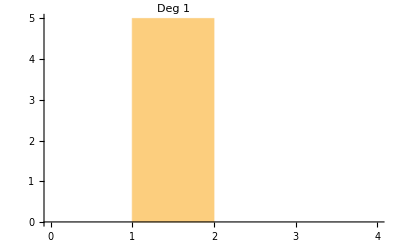
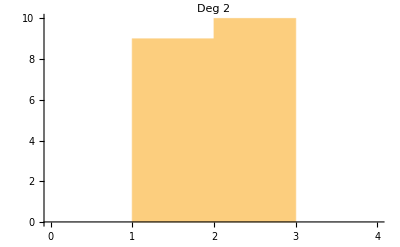
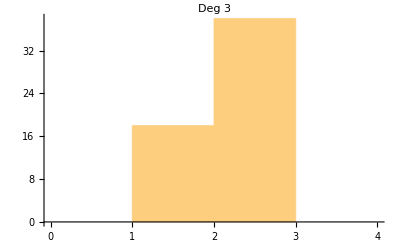
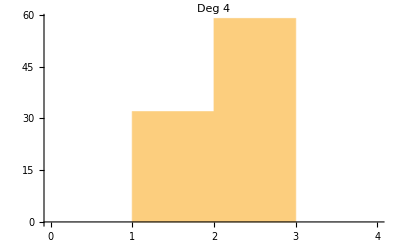
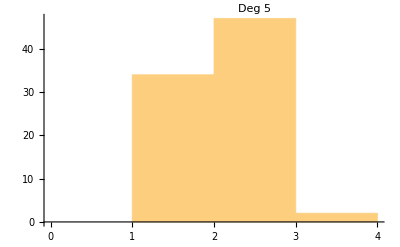
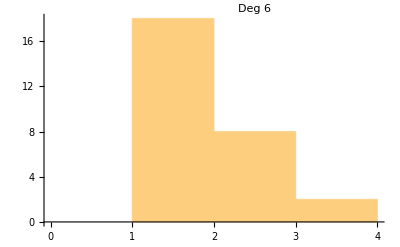

The number of non-zero coeff totals 282.

```mathematica
(* u > 0 *) 
Print[" 
Checking that u = a2*a3 - a4*a1 > 0: "]
u = Expand[a2*a3-a4*a1] ;
coeff = CoefficientArrays[u, Variables[u]]; 


For[i=1, i <= Length[coeff], i++, (* Printing min/max coefficients *)
If[i==1,
Print[StringForm["The constant term is ``.", coeff[[1]]]];
];
If[i>1,
Print[StringForm["For deg `` terms, the min coefficient is ``, min-nonzero is ``, and max is ``.", i-1,  Min[coeff[[i]]],  Min[coeff[[i]]["NonzeroValues"]],  Max[coeff[[i]]]]]
];
]

plist = {}; 
For[i=1, i<= Length[coeff], i++,  (*Generating histograms on distribution of coeff*)
If[ Max[coeff[[i]]]== 0 ,
Print[StringForm["Empty histogram not generated for deg ``.", i-1]]; 
]; 
If[Max[coeff[[i]]]!= 0,
p =  Histogram[coeff[[i]]["NonzeroValues"], {0,4,1}, ChartLabels->Placed[StringForm["Deg ``", i-1], Above]] ;
AppendTo[plist, p]; 
];
]
Print["Generating all histograms:"]; 
Print[plist]

(* Count number of coefficients *)
NumOfCoeff = 0; 
If[coeff[[1]]!=0,
NumOfCoeff = 1; 
];
For[i=2,i<=Length[coeff], i++,
NumOfCoeff = NumOfCoeff + Length[coeff[[i]]["NonzeroValues"]];
]
StringForm["The number of non-zero coeff totals ``.", NumOfCoeff]

Clear[coeff, plist];
```

Checking that v = u*a1 - a3^2*a0 > 0:

The constant term is 0.

For deg 1 terms, the min coefficient is 0, min-nonzero is ∞, and max is 0.

For deg 2 terms, the min coefficient is 0, min-nonzero is ∞, and max is 0.

For deg 3 terms, the min coefficient is 0, min-nonzero is 1, and max is 2.

For deg 4 terms, the min coefficient is 0, min-nonzero is 1, and max is 8.

For deg 5 terms, the min coefficient is 0, min-nonzero is 1, and max is 16.

For deg 6 terms, the min coefficient is 0, min-nonzero is 1, and max is 16.

For deg 7 terms, the min coefficient is 0, min-nonzero is 1, and max is 18.

For deg 8 terms, the min coefficient is 0, min-nonzero is 1, and max is 20.

For deg 9 terms, the min coefficient is 0, min-nonzero is 1, and max is 18.

For deg 10 terms, the min coefficient is 0, min-nonzero is 1, and max is 20.

For deg 11 terms, the min coefficient is 0, min-nonzero is 1, and max is 10.

For deg 12 terms, the min coefficient is 0, min-nonzero is 1, and max is 5.

Empty histogram not generated for deg 0.

Empty histogram not generated for deg 1.

Empty histogram not generated for deg 2.

Generating all histograms:

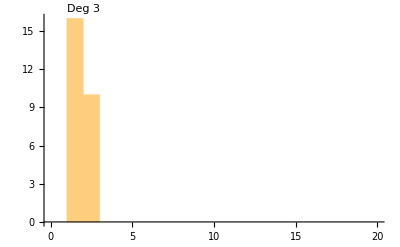
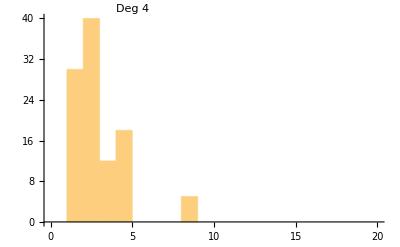
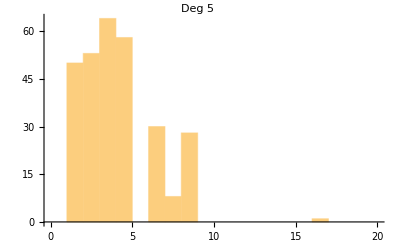
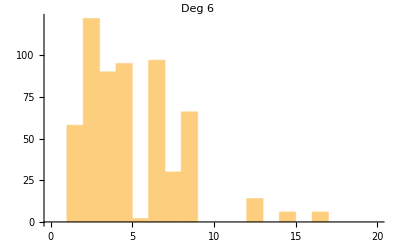
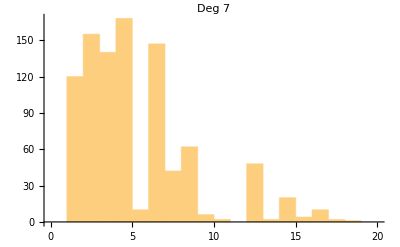
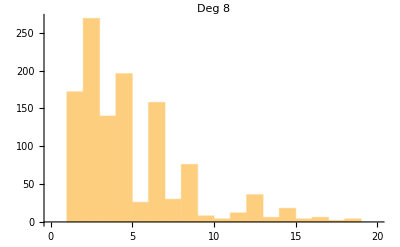
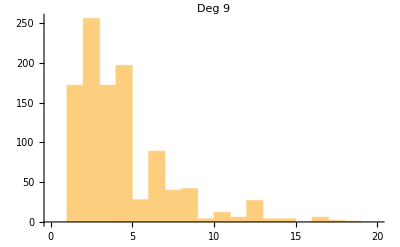
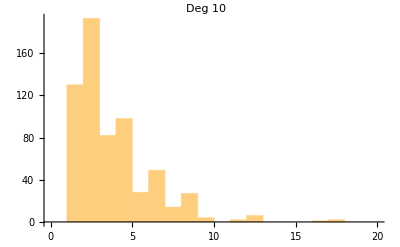

The number of non-zero coeff totals 5091.

```mathematica
(* v > 0 *) 
Print[" 
Checking that v = u*a1 - a3^2*a0 > 0: "]
v = Expand[u*a1-a3^2*a0] ;
coeff = CoefficientArrays[v, Variables[v]]; 


For[i=1, i <= Length[coeff], i++, (*Printing min/max coefficients*)
If[i==1,
Print[StringForm["The constant term is ``.", coeff[[1]]]];
];
If[i>1,
Print[StringForm["For deg `` terms, the min coefficient is ``, min-nonzero is ``, and max is ``.", i-1,  Min[coeff[[i]]],  Min[coeff[[i]]["NonzeroValues"]],  Max[coeff[[i]]]]]
];
]

plist = {}; 
For[i=1, i<= Length[coeff], i++,  (*Generating histograms on distribution of coeff*)
If[ Max[coeff[[i]]]== 0 ,
Print[StringForm["Empty histogram not generated for deg ``.", i-1]]; 
]; 
If[Max[coeff[[i]]]!= 0,
p =  Histogram[coeff[[i]]["NonzeroValues"], {0,20,1}, ChartLabels->Placed[StringForm["Deg ``", i-1], Above]] ;
AppendTo[plist, p]; 
];
]
Print["Generating all histograms:"]; 
Print[plist]

(* Count number of coefficients *)
NumOfCoeff = 0; 
If[coeff[[1]]!=0,
NumOfCoeff = 1; 
];
For[i=2,i<=Length[coeff], i++,
NumOfCoeff = NumOfCoeff + Length[coeff[[i]]["NonzeroValues"]];
]
StringForm["The number of non-zero coeff totals ``.", NumOfCoeff]


Clear[coeff, plist];
```